## Model function

```mathematica
ClearAll["Global`*"]
```

```mathematica
Clear[Tmax,z,rmax,β,θ1,θ2,τ,m,σ]
```

```mathematica
EvolvingKevinStochastic[Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_,processerror_]:=Block[{},
(* Initialize variables *)
N1=Array[0&,Tmax+1];
N2=Array[0&,Tmax+1];
x1=Array[0&,Tmax+1];
x2=Array[0&,Tmax+1];
N1[[1]]=2;N2[[1]]=2;x1[[1]]=initμ1;x2[[1]]=initμ2;
(* Trait distributions *)
p1[x_,μ1_]=PDF[NormalDistribution[μ1,σ],x];
p2[x_,μ2_]=PDF[NormalDistribution[μ2,σ],x];

(* Average fitness W of individuals with traits x *)
(* Integrate[α[rmax,x,τ,θ]*(w p1[x,μ1,1]+(1-w)p2[x,μ2,1]),{x,-∞,∞}], then take derivatives with respect to μ1 and μ2 to get *)
meanFit1=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1];
meanFit2=D[Log[(1-w)(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+w(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2];

(* Calculate reproductive rates: outside of loop and init for speed *)
(*r1Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r1Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
r1Site1=(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site1=(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2));r1Site2=(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site2=(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));
(* Simulation loop *)
Table[
(* Calculate reprod using mixture distribution after migration *)
r1Site1EQ=r1Site1/.{μ1->x1[[i]]};r2Site1EQ=r2Site1/.{μ2->x2[[i]]};r1Site2EQ=r1Site2/.{μ1->x1[[i]]};r2Site2EQ=r2Site2/.{μ2->x2[[i]]};
(* Find biomass at time t+1 *)
(* It now takes into account the fact that a fraction of the population leaves the site as -m N1[[i]] *)
N1[[i+1]]=
((1-m)N1[[i]]+m N2[[i]])ⅇ^-z+
((r1Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])*(N1[[i]]-m N1[[i]])+ ((r2Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])*m N2[[i]]))ⅇ^(-β((1-m)N1[[i]]+m N2[[i]])); 
N2[[i+1]]=
((1-m)N2[[i]]+m N1[[i]])ⅇ^-z+
((r2Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* (N2[[i]]-m N2[[i]])+(r1Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* m N1[[i]])ⅇ^(-β((1-m)N2[[i]]+m N1[[i]]));
(* Find mean trait value at time t+1 *)
x1[[i+1]]=σ^2(w x1[[i]]+(1-w)x2[[i]]+meanFit1)/.{θ->θ1,μ1->x1[[i]],μ2->x2[[i]],w->(N1[[i]]-m N1[[i]])/(N1[[i]]+m N2[[i]]-m N1[[i]])};
x2[[i+1]]=σ^2(w x2[[i]]+(1-w)x1[[i]]+meanFit2)/.{θ->θ2,μ1->x1[[i]],μ2->x2[[i]],w->(N2[[i]]- m N2[[i]])/(m N1[[i]]+N2[[i]]- m N2[[i]])};
,{i,1,Tmax}];
toplotN1=Table[{i,N1[[i]]},{i,1,Tmax}];
toplotN2=Table[{i,N2[[i]]},{i,1,Tmax}];
toplotx1=Table[{i,x1[[i]]},{i,1,Tmax}];
toplotx2=Table[{i,x2[[i]]},{i,1,Tmax}];

]
```

```mathematica
(* N1, N2, X1, X2 against m *)
(*Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_*)
Reps=200;
mig=Table[x,{x,0,1,1/Reps}];
MinN1=Array[0.  # &,Reps];MaxN1=Array[0.  # &,Reps];MeanN1=Array[0.  # &,Reps];
MinN2=Array[0.  # &,Reps];MaxN2=Array[0.  # &,Reps];MeanN2=Array[0.  # &,Reps];
SDN1=Array[0.  # &,Reps];SDN2=Array[0.  # &,Reps];
PE=Array[0.  # &,Reps];
Minx1=Array[0.  # &,Reps];Maxx1=Array[0.  # &,Reps];Meanx1=Array[0.  # &,Reps];
Minx2=Array[0.  # &,Reps];Maxx2=Array[0.  # &,Reps];Meanx2=Array[0.  # &,Reps];
Timing[Table[EvolvingKevinStochastic[
(*Tmax*)tmax=1000,
(*z*)0.5,
(*rmax*)2,
(*β*)0.001,
(*θ1*)theta1=5,
(*θ2*)theta2=10,
(*initμ1*)5,
(*initμ2*)10,
(*τ*)1,
(*σ*)1,
(*m*)mig[[i]],
(*processerror*)0.00];
burnin=0.9;
MinN1[[i]]=Min[N1];MaxN1[[i]]=Max[N1];MeanN1[[i]]=Mean[N1[[Floor[tmax*burnin];;tmax]]];
MinN2[[i]]=Min[N2];MaxN2[[i]]=Max[N2];MeanN2[[i]]=Mean[N2[[Floor[tmax*burnin];;tmax]]];
SDN1[[i]]=StandardDeviation[N1[[Floor[tmax*burnin];;tmax]]];SDN2[[i]]=StandardDeviation[N2[[Floor[tmax*burnin];;tmax]]];
PE[[i]] = (Mean[{StandardDeviation[N1[[Floor[tmax*burnin];;tmax]]],StandardDeviation[N2[[Floor[tmax*burnin];;tmax]]]}]/ Mean[{Mean[N1[[Floor[tmax*burnin];;tmax]]],Mean[N2[[Floor[tmax*burnin];;tmax]]]}])*(1/(StandardDeviation[N1[[Floor[tmax*burnin];;tmax]]+N2[[Floor[tmax*burnin];;tmax]]]/Mean[N1[[Floor[tmax*burnin];;tmax]]+N2[[Floor[tmax*burnin];;tmax]]]));
Minx1[[i]]=Min[x1];Maxx1[[i]]=Max[x1];Meanx1[[i]]=Mean[x1[[Floor[tmax*burnin];;tmax]]];
Minx2[[i]]=Min[N2];Maxx2[[i]]=Max[x2];Meanx2[[i]]=Mean[x2[[Floor[tmax*burnin];;tmax]]];
,{i,1,Reps}];
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{117.89,Null}

```mathematica
toplotN1=Table[{mig[[i]],MeanN1[[i]]},{i,1,Reps}];
toplotN2=Table[{mig[[i]],MeanN2[[i]]},{i,1,Reps}];
toplotx1=Table[{mig[[i]],theta1-Meanx1[[i]]},{i,1,Reps}];
toplotx2=Table[{mig[[i]],theta2-Meanx2[[i]]},{i,1,Reps}];
toplotPE=Table[{mig[[i]],PE[[i]]},{i,1,Reps}];
toplotSD1=Table[{mig[[i]],SDN1[[i]]},{i,1,Reps}];
toplotSD2=Table[{mig[[i]],SDN2[[i]]},{i,1,Reps}];
toplotMPE1=Table[{MeanN1[[i]],PE[[i]]},{i,1,Reps}];
toplotMPE2=Table[{MeanN2[[i]],PE[[i]]},{i,1,Reps}];
toplotMPEAgg=Table[{MeanN1[[i]]+MeanN2[[i]],PE[[i]]},{i,1,Reps}];
```

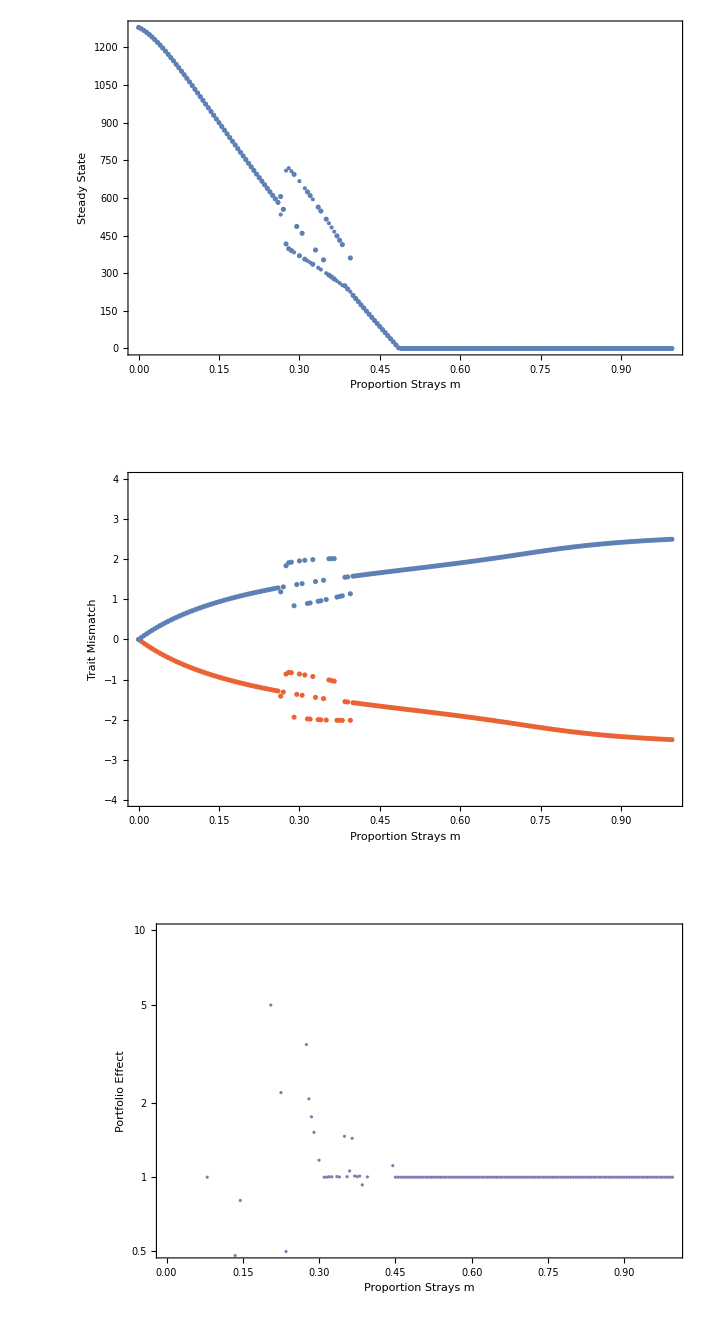

```mathematica
(* Mean density against m *)
mPlot=GraphicsGrid[{{
Show[
ListPlot[{toplotN1,toplotN2},PlotStyle->ColorData[97,1], PlotRange->{0.000000001,All}, Joined->False,Frame->True,FrameLabel->{"Proportion Strays m","Steady State"}],
ListPlot[toplotN2, Joined->False, PlotRange->All,ImageSize->250]
]},{
(* Mean mismatch against m *)
Show[
ListPlot[toplotx1,PlotStyle->ColorData[97,4], PlotRange->{-4,4}, Joined->False,Frame->True,FrameLabel->{"Proportion Strays m","Trait Mismatch"}],
ListPlot[toplotx2, Joined->False, PlotRange->All,ImageSize->250]
]},{
(* Portfolio Effect against m *)
Show[
Show[
ListLogPlot[toplotPE,PlotStyle->ColorData[97,5], PlotRange->{0.5,10}, Joined->False,Frame->True,FrameLabel->{"Proportion Strays m","Portfolio Effect"},PlotRange->All,ImageSize->250](*,
ListLogPlot[MovingAverage[toplotPE,100],Joined->True,PlotStyle->Directive[ColorData[97,5],Thickness[0.003]]]*)
]
]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_Density_sig16.pdf"}],mPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_Density_sig16.pdf

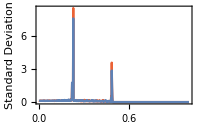

```mathematica
Show[
ListPlot[toplotSD1,PlotStyle->ColorData[97,4], PlotRange->All, Joined->True,Frame->True,FrameLabel->{"Proportion Strays m","Standard Deviation"},PlotRange->All,ImageSize->250],
ListPlot[toplotSD2, PlotRange->All, Joined->True,Frame->True,FrameLabel->{"Proportion Strays m","Standard Deviation of S.S."},PlotRange->All,ImageSize->250]]
```

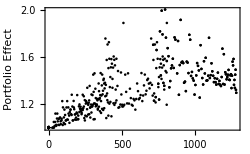

```mathematica
Show[
ListPlot[toplotMPE2,PlotStyle->Black, PlotRange->{1,2}, Joined->False,Frame->True,FrameLabel->{"Mean Steady State","Portfolio Effect"},PlotRange->All,ImageSize->250],
ListPlot[toplotMPE1,PlotStyle->Black, PlotRange->{1,2}, Joined->False,Frame->True,FrameLabel->{"Mean Steady State","Portfolio Effect"},PlotRange->All,ImageSize->250]
]
```

### Individual Trajectory

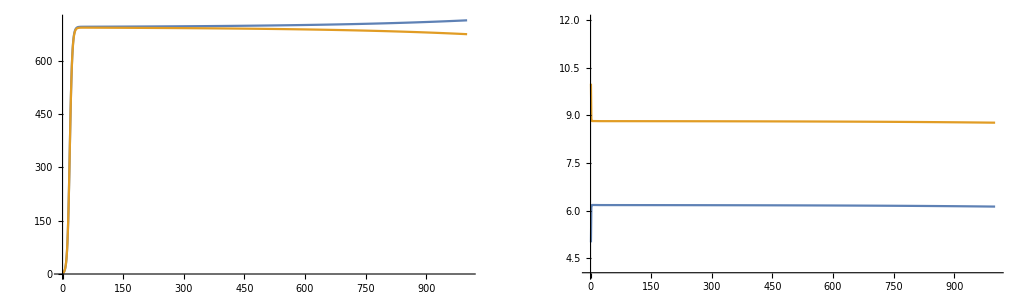

```mathematica
out=EvolvingKevinStochastic[
(*Tmax*)tmax=1000,
(*z*)0.5,
(*rmax*)2,
(*β*)0.001,
(*θ1*)theta1=5,
(*θ2*)theta2=10,
(*initμ1*)5-0.001,
(*initμ2*)10,
(*τ*)1,
(*σ*)1,
(*m*)0.22,
(*processerror*)0.000
]
GraphicsGrid[{{
ListPlot[{N1,N2},Joined->True,PlotRange->{0,All}],
ListPlot[{x1,x2},Joined->True,PlotRange->{4,12}]
}}]
```

```mathematica
StandardDeviation[N1[[Floor[tmax*burnin];;tmax]]]
```

2.53518

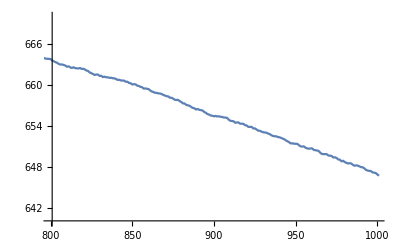

```mathematica
ListPlot[{N1,N2},Joined->True,PlotRange->{{800,1000},{640,670}}]
```

```mathematica
PE
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,47.3994,511.621,239.631,68.5078,3.70481,32.9038,1.78377,1.05013,1.09301,1.02873,1.00521,1.05776,1.18172,1.10145,1.0181,1.01388,1.01252,1.02091,1.16928,1.00814,1.09769,1.00656,1.00336,1.02925,1.0005,1.00017,1.,1.,1.,1.,1.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

$Aborted